```mathematica
A ={{-a,0},{0,0}}//MatrixForm
```

(-a | 0
0 | 0)

```mathematica
B = {{3,0,0,0},{-1,0,0,0},{-1,0,0,0},{-1,0,0,0}} // MatrixForm
```

(3 | 0 | 0 | 0
-1 | 0 | 0 | 0
-1 | 0 | 0 | 0
-1 | 0 | 0 | 0)

```mathematica
TensorProduct[{{a0,0},{0,0}},{{0,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}] // MatrixForm
```

((0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -a0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -a0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -a0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -a0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0))

```mathematica
{{-b,0,0,0}}//MatrixForm
```

(-b | 0 | 0 | 0)

```mathematica
{{-2,0,0,0},{1,0,0,0},{1,0,0,0},{0,0,0,0}}// MatrixForm
```

(-2 | 0 | 0 | 0
1 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Matrix for 2 sites cooperativity model

```mathematica
Clear[μ]
```

```mathematica
J=0;
μi=0;
```

```mathematica
α0 = 0.5(1-Tanh[-μi/2]);
β0 = 0.5(1-Tanh[μi/2]);
α1 = 0.5(1-Tanh[-(J +μi)/2]);
β1 = 0.5(1-Tanh[(J +μi)/2]);
```

```mathematica
Row1 = {-2α0, β0,β0,0};
Row2 = {α0,-β0-α1,0,β1};
Row3 ={α0,0,-β0-α1,β1};
Row4 = {0,α1,α1,-2β1};
```

```mathematica
(M2 = {Row1,Row2,Row3,Row4}) //MatrixForm
```

(-1. | 0.5 | 0.5 | 0
0.5 | -1. | 0 | 0.5
0.5 | 0 | -1. | 0.5
0 | 0.5 | 0.5 | -1.)

```mathematica
DiagonalizableMatrixQ[M2]
```

True

```mathematica
Eigenvalues[M2 ];
Eigenvectors[M2 ];
```

```mathematica
(U = Transpose[Eigenvectors[M2]]) // MatrixForm;
(Ui= Inverse[U]) // MatrixForm;
```

```mathematica
Λ = Ui.M2.U // Chop//MatrixForm
```

(-2. | 0 | 0 | 0
0 | -1. | 0 | 0
0 | 0 | -1. | 0
0 | 0 | 0 | 0)

```mathematica
solDiago[t_]:=Table[c[k]*Exp[Eigenvalues[M2][[k]]*t],{k,1,Length[M2]}]
```

```mathematica
solDiago[t]//MatrixForm
```

(ⅇ^(-2. t) c[1]
ⅇ^(-1. t) c[2]
ⅇ^(-1. t) c[3]
ⅇ^(3.33067×10^-16 t) c[4])

```mathematica
(solOri=U.solDiago[t])//MatrixForm;
```

```mathematica
(IC=solOri/. t-> 0)//MatrixForm;
```

```mathematica
resCond=Solve[Table[IC[[k]]==If[k==1,1,0],{k,Length[IC]}],Table[c[k],{k,1,Length[IC]}]];
```

```mathematica
solSpecial = solOri/.resCond//Flatten;
```

```mathematica
Sum[solSpecial[[k]],{k,1,Length[solSpecial]}]/.t->100
```

1.

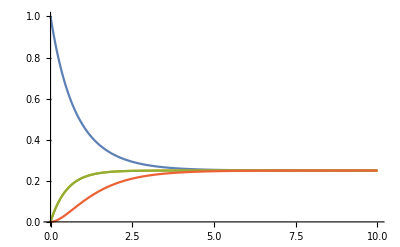

```mathematica
Tmax=10;
Plot[{solSpecial},{t,0,Tmax},PlotRange->{{0,Tmax},{0,1}}]
```

```mathematica
Nmax=2;
```

```mathematica
resCond=Solve[Table[IC[[k]]==If[k==Nmax+2,1,0],{k,Length[IC]}],Table[c[k],{k,1,Length[IC]}]]
```

{{c[1]→0.5,c[2]→0.,c[3]→0.707107,c[4]→-0.5}}

```mathematica
solSpecialStall = solOri/.resCond//Flatten;
```

```mathematica
Sum[solSpecialStall[[k]],{k,1,Length[solSpecial]}]/.t->100
```

1.

```mathematica
Tmax=10;
```

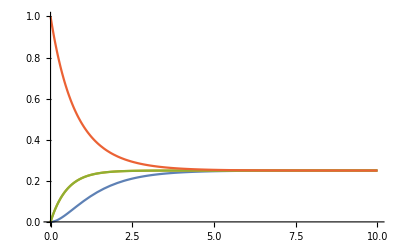

```mathematica
Plot[{solSpecialStall},{t,0,Tmax},PlotRange->{{0,Tmax},{0,1}}]
```

```mathematica
solSpecial/. t-> 100000//MatrixForm
```

General::munfl: Exp[-200000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-100000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(0.25
0.25
0.25
0.25)

```mathematica
m[t_]:=Sum[solSpecial[[k]]*(k-1),{k,1,Length[solSpecial]}]
```

```mathematica
mr[t_] := solSpecial[[1]]*0+solSpecial[[2]]*1+solSpecial[[3]]*1+solSpecial[[4]]*2
```

```mathematica
sd[t_]:=Sqrt[Sum[solSpecial[[k]]*(k-1)^2,{k,1,Length[solSpecial]}]-m[t]^2]
```

```mathematica
mStall[t_]:=Sum[solSpecialStall[[k]]*(k-1),{k,1,Length[solSpecialStall]}]
mrStall[t_] := solSpecialStall[[1]]*0+solSpecialStall[[2]]*1+solSpecialStall[[3]]*1+solSpecialStall[[4]]*2
```

```mathematica
sdStall[t_]:=Sqrt[Sum[solSpecialStall[[k]]*(k-1)^2,{k,1,Length[solSpecialStall]}]-mStall[t]^2]
```

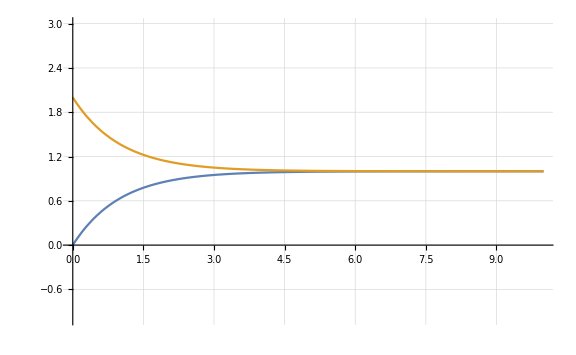

```mathematica
Tmax=10;
plot=Show[Plot[{mr[t],mrStall[t]},{t,0,Tmax},PlotRange->{{0,Tmax},{-1,Nmax+1}},GridLines->Automatic, TargetUnits->"Minutes"],ImageSize->Large]
```

### Matrix for 3 sites cooperativity model

```mathematica
Clear[μ]
```

```mathematica
J=1;
μi=-0.5;
```

```mathematica
α0 = 0.5(1-Tanh[-μi/2]);
β0 = 0.5(1-Tanh[μi/2]);
α1 = 0.5(1-Tanh[-(J +μi)/2]);
β1 = 0.5(1-Tanh[(J +μi)/2]);
α2 = 0.5(1-Tanh[-J -μi/2]);
β2 = 0.5(1-Tanh[J +μi/2]);
```

```mathematica
Row1 = {-3α0, β0,β0,β0,0,0,0,0};
Row2 = {α0,-β0-2α1,0,0,β1,0,β1,0};
Row3 ={α0,0,-β0-2α1,0,β1,β1,0,0};
Row4 = {α0,0,0,-β0-2α1,0,β1,β1,0};
Row5 = {0,α1,α1,0,-α2-2β1,0,0,β2};
Row6 = {0,0,α1,α1,0,-α2-2β1,0,β2};
Row7 = {0,α1,0,α1,0,0,-α2-2β1,β2};
Row8 = {0,0,0,0,α2,α2,α2,-3β2};
```

```mathematica
(M3 = {Row1,Row2,Row3,Row4,Row5,Row6,Row7,Row8}) //MatrixForm
```

(-1.13262 | 0.622459 | 0.622459 | 0.622459 | 0 | 0 | 0 | 0
0.377541 | -1.86738 | 0 | 0 | 0.377541 | 0 | 0.377541 | 0
0.377541 | 0 | -1.86738 | 0 | 0.377541 | 0.377541 | 0 | 0
0.377541 | 0 | 0 | -1.86738 | 0 | 0.377541 | 0.377541 | 0
0 | 0.622459 | 0.622459 | 0 | -1.57266 | 0 | 0 | 0.182426
0 | 0 | 0.622459 | 0.622459 | 0 | -1.57266 | 0 | 0.182426
0 | 0.622459 | 0 | 0.622459 | 0 | 0 | -1.57266 | 0.182426
0 | 0 | 0 | 0 | 0.817574 | 0.817574 | 0.817574 | -0.547277)

```mathematica
DiagonalizableMatrixQ[M3]
```

True

```mathematica
Eigenvalues[M3 ] //Chop;
Eigenvectors[M3 ]//Chop;
```

```mathematica
(U = Transpose[Eigenvectors[M3]]) // MatrixForm;
(Ui= Inverse[U]) // MatrixForm;
```

```mathematica
Λ = Ui.M3.U // Chop//MatrixForm
```

(-3. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2.22669 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2.22669 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1.55015 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.21334 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1.21334 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.56978 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
solDiago[t_]:=Table[c[k]*Exp[Eigenvalues[M3][[k]]*t],{k,1,Length[M3]}]
```

```mathematica
solDiago[t]//Chop//MatrixForm
```

(ⅇ^(-3. t) c[1]
ⅇ^(-2.22669 t) c[2]
ⅇ^(-2.22669 t) c[3]
ⅇ^(-1.55015 t) c[4]
ⅇ^(-1.21334 t) c[5]
ⅇ^(-1.21334 t) c[6]
ⅇ^(-0.56978 t) c[7]
c[8])

```mathematica
(solOri=U.solDiago[t])//MatrixForm;
```

```mathematica
(IC=solOri/. t-> 0)//MatrixForm;
```

```mathematica
resCond=Solve[Table[IC[[k]]==If[k==1,1,0],{k,Length[IC]}],Table[c[k],{k,1,Length[IC]}]];
```

```mathematica
solSpecial = solOri/.resCond//Flatten;
```

```mathematica
Sum[solSpecial[[k]],{k,1,Length[solSpecial]}]/.t->100
```

1.

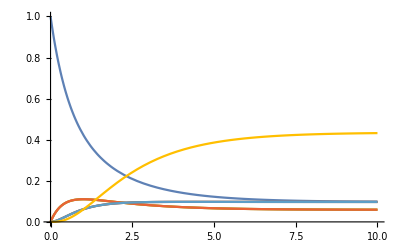

```mathematica
Tmax=10;
Plot[{solSpecial},{t,0,Tmax},PlotRange->{{0,Tmax},{0,1}}]
```

```mathematica
Nmax=3;
```

```mathematica
resCond=Solve[Table[IC[[k]]==If[k==2*Nmax+2,1,0],{k,Length[IC]}],Table[c[k],{k,1,Length[IC]}]]
```

{{c[1]→0.0688284,c[2]→6.68036×10^-17,c[3]→-2.86049×10^-18,c[4]→-0.242593,c[5]→-3.42295×10^-16,c[6]→-2.21678×10^-17,c[7]→-0.428235,c[8]→0.487209}}

```mathematica
solSpecialStall = solOri/.resCond//Flatten;
```

```mathematica
Sum[solSpecialStall[[k]],{k,1,Length[solSpecial]}]/.t->100
```

1.

```mathematica
Tmax=10;
```

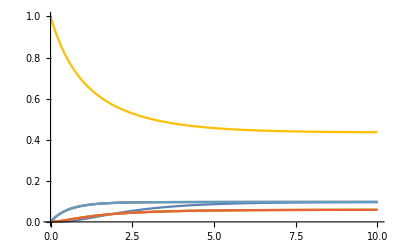

```mathematica
Plot[{solSpecialStall},{t,0,Tmax},PlotRange->{{0,Tmax},{0,1}}]
```

```mathematica
solSpecial/. t-> 1000//MatrixForm
```

General::munfl: Exp[-3000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2226.69] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(0.0970753
0.0588791
0.0588791
0.0588791
0.0970753
0.0970753
0.0970753
0.435061)

```mathematica
m[t_]:=Sum[solSpecial[[k]]*(k-1),{k,1,Length[solSpecial]}]
mr[t_] := solSpecial[[1]]*0+solSpecial[[2]]*1+solSpecial[[3]]*1+solSpecial[[4]]*1+solSpecial[[5]]*2 + solSpecial[[6]]*2 + solSpecial[[7]]*2 + solSpecial[[8]]*3
```

```mathematica
sd[t_]:=Sqrt[Sum[solSpecial[[k]]*(k-1)^2,{k,1,Length[solSpecial]}]-m[t]^2]
```

```mathematica
mStall[t_]:=Sum[solSpecialStall[[k]]*(k-1),{k,1,Length[solSpecialStall]}]
mrStall[t_] := solSpecialStall[[1]]*0+solSpecialStall[[2]]*1+solSpecialStall[[3]]*1+solSpecialStall[[4]]*1+solSpecialStall[[5]]*2 + solSpecialStall[[6]]*2 + solSpecialStall[[7]]*2 + solSpecialStall[[8]]*3
```

```mathematica
sdStall[t_]:=Sqrt[Sum[solSpecialStall[[k]]*(k-1)^2,{k,1,Length[solSpecialStall]}]-mStall[t]^2]
```

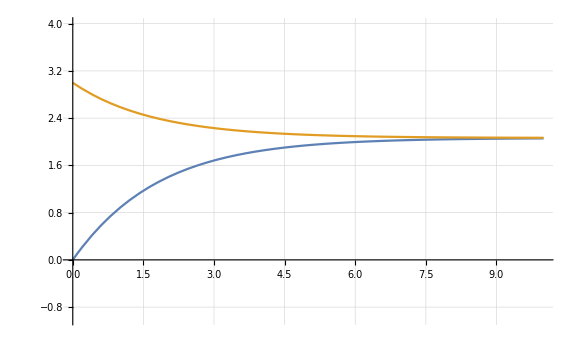

```mathematica
Tmax=10;
plot=Show[Plot[{mr[t],mrStall[t]},{t,0,Tmax},PlotRange->{{0,Tmax},{-1,Nmax+1}},GridLines->Automatic, TargetUnits->"Minutes"],ImageSize->Large]
```

```mathematica
Ns[t_,Nss_,n0_,τ_]:= Nss + (n0 - Nss)Exp[-t/τ];
```

```mathematica
dataRes = Table[mr[t],{t,0,10}];
```

```mathematica
FindFit[dataRes,Ns[t,Nss,n0,τres],{Nss,n0,τres},t]
```

{Nss→2.06642,n0→-1.55428,τres→1.78565}

```mathematica
{n0,Nss,τres}/.{Nss->2.066421308052998,n0->-1.5542837641485672,τres->1.7856499328132578}
```

{-1.55428,2.06642,1.78565}

```mathematica
FindFit[Table[mrStall[t],{t,0,10}],Ns[t,Nss,n0,τrel],{Nss,n0,τrel},t]
```

{Nss→2.06495,n0→3.72895,τrel→1.73329}

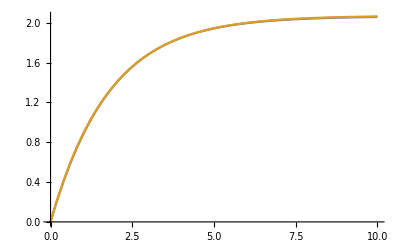

```mathematica
Plot[{mr[t],Ns[t,2.07,0,1.785]},{t,0,10}]
```

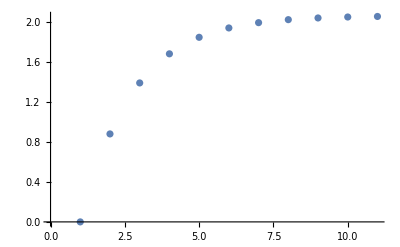

```mathematica
ListPlot[dataRes]
```